-1+2 x Cos[x-y]

Cos[x+y]+4 Sin[x y]

2 Cos[x-y]-2 x Sin[x-y]

2 x Sin[x-y]

4 y Cos[x y]-Sin[x+y]

4 x Cos[x y]-Sin[x+y]

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→0.927999,y→-0.197863}

-0.201182

0.0147358

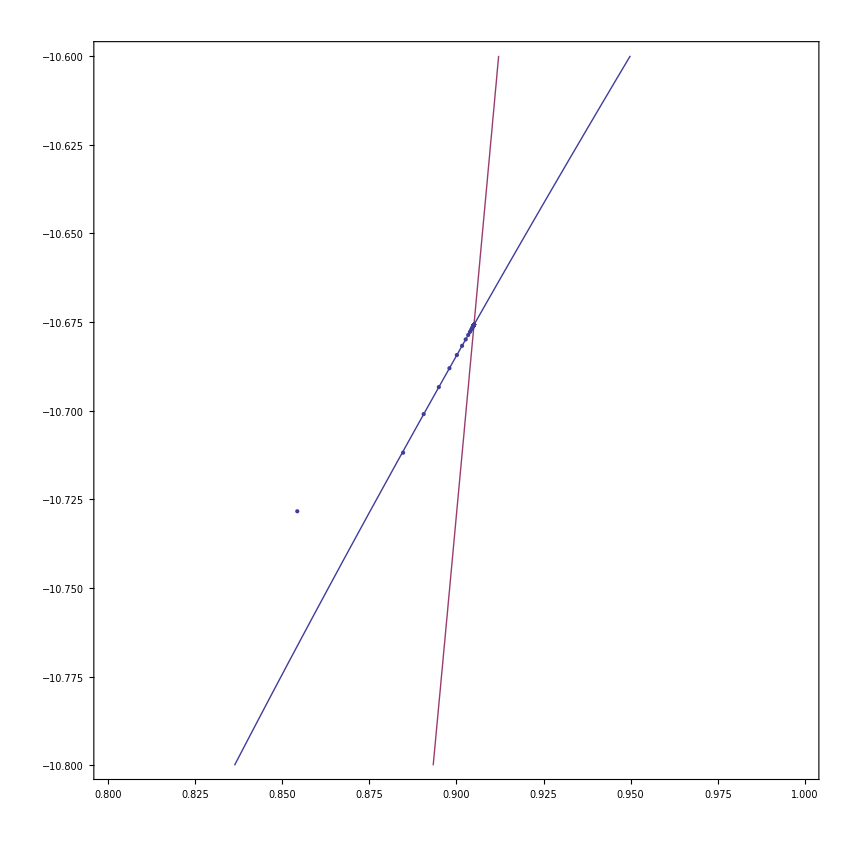

```mathematica
(*f = 2*x*(Cos[x]*Cos[y] - Sin[x]*Sin[y])-1*)
(*g =Cos[x]Cos[y] + Sin[x]Sin[y] + 4Sin[x*y]*)
f = 2*x* Cos[x - y]  - 1
g = Cos[x + y] + 4Sin[x*y]
(*f = 9*x^2+4*y^2 - 36*)
(*g = 3*x+2*y - 6*)
c = ContourPlot[{f==0, g==0}, {x,0.8,1}, {y, -10.8,-10.6}];

D[f, x]
D[f, y]
D[g,x]
D[g,y]
(*{res,{evx}}=Reap[FindRoot[{f, g},{{x, 1}, {y,1}},Method->"Newton", EvaluationMonitor:>Sow[{x, y}]]]*)
r = FindRoot[{f, g}, {{x, 1}, {y,1}}, Method->"Newton"]
(*Plug both roots back in*)
f /. r
g/. r
p = Graphics[{PointSize[.009],  Point[{x, y} /. r]}];
p = Graphics[{PointSize[.009], Point[{0.81091,8.00041}]}];
p3 = Graphics[{PointSize[.009], Point[{-0.8528906,7.627503}]}];
p2 =ListPlot[{{0.500000,-10.567187},{0.985278,-10.943119},{0.734664,-11.040088},{0.854365,-10.728391},{0.884728,-10.711871},{0.890621,-10.700995},{0.894965,-10.693385},{0.898014,-10.688060},{0.900150,-10.684340},{0.901641,-10.681746},{0.902682,-10.679939},{0.903406,-10.678682},{0.903909,-10.677809},{0.904259,-10.677202},{0.904502,-10.676781},{0.904671,-10.676489},{0.904788,-10.676286},{0.904869,-10.676145},{0.904925,-10.676048},{0.904964,-10.675980},{0.904991,-10.675933},{0.905010,-10.675901},{0.905023,-10.675878},{0.905032,-10.675862},{0.905039,-10.675852},{0.905043,-10.675844},{0.905046,-10.675839},{0.905048,-10.675835},{0.905049,-10.675833},{0.905050,-10.675831},{0.905051,-10.675830},{0.905052,-10.675829},{0.905052,-10.675828},{0.905052,-10.675828},{0.905052,-10.675828},{0.905052,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827},{0.905053,-10.675827}}];
Show[c, p2]
```

```mathematica
-1+2 x (Cos[x] Cos[y]-Sin[x] Sin[y]) /. {x->3.212526,y->-3.232637}
```

5.42375

```mathematica
Cos[x] Cos[y]+Sin[x] Sin[y]+4 Sin[x y] /. {x->3.212526,y->-3.232637}
```

4.26403

```mathematica
2 x (-Cos[y] Sin[x]-Cos[x] Sin[y])+2 (Cos[x] Cos[y]-Sin[x] Sin[y]) /. {x->3.212526,y->-3.232637}
```

2.1288

```mathematica
2 x (-Cos[y] Sin[x]-Cos[x] Sin[y]) /. {x->3.212526,y->-3.232637}
```

0.129206

```mathematica
4 y Cos[x y]-Cos[y] Sin[x]+Cos[x] Sin[y] /. {x->3.212526,y->-3.232637}
```

7.25304

```mathematica
4 x Cos[x y]+Cos[y] Sin[x]-Cos[x] Sin[y] /. {x->3.212526,y->-3.232637}
```

-7.20692

```mathematica
2 x (-Cos[y] Sin[x]-Cos[x] Sin[y])+2 (Cos[x] Cos[y]-Sin[x] Sin[y]) /. {x->3.212526,y->-3.232637}
```

2.1288

```mathematica
4 y Cos[x y]-Cos[y] Sin[x]+Cos[x] Sin[y] /.{x->3.212526,y->-3.232637}
```

7.25304

```mathematica
4 x Cos[x y]+Cos[y] Sin[x]-Cos[x] Sin[y] /.{x->3.212526,y->-3.232637}
```

-7.20692

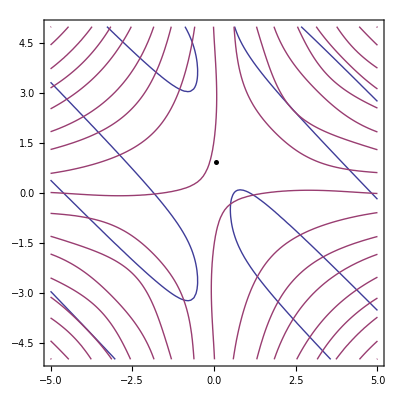

FindRootPlot[{x^2-3 y,Sin[x^2+y^2]},{{x,1},{y,1}}]